## Summary

This week, I’ve constructed derivatives that can be “easily” implemented in C. I’ve successfully tested the analytical derivatives with the numerical results for subsets of cells without the cells on the boundary. However, I have not build the functions for the cells on the boundary. I have not really looked into the (d^2 e)/dgamma^2 for those cells, but I’ll do it if necessary. I’ve started to build the functions in C with the assumptions that every vertex is determined by three cell centers  (hence no vertices imposed by the boundary).

## Numerical derivatives

```mathematica
(*/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc*)
(*./Learning/Research/G_T/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc*)
```

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_datastructure.nc","Datasets"]
```

{/d2Edgammadgamma}

```mathematica
test=Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_datastructure.nc","Data"];
```

```mathematica
test[[1,8,1]]
```

68.9303

```mathematica
getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[7,1]]]/2;
frames=Length[t[[2]]];
times=Flatten[t[[2]]];
positions={};
Do[
posSet=t[[7,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];
(*getData[fname_]:=Module[{t,n,frames,types,times,positions,posSet},
t=Import[fname,"Data"];
n=Length[t[[1,1]]]/2;Table[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.001,1,1,1,3.8],{i,100}]
frames=Length[t[[1]]];
times=Flatten[t[[1]]];
types=t[[3,1]];
positions={};
Do[
posSet=t[[1,fr]];
AppendTo[positions,Table[{posSet[[2*i+1]],posSet[[2*i+2]]},{i,0,n-1}]];
,{fr,1,frames}];
{n,frames,positions,types,times}];*)
```

```mathematica
temp=getData["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/analysescript/test_N1000_p3.80000_T0.00010000_et0.000000.nc"];
p=temp[[3,Length[temp[[3]]]]];
min=Min[p]-.1;max=Max[p]+.1;
vm=VoronoiMesh[p,{{min,max},{min,max}}];
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

```mathematica
centroids=RegionCentroid/@MeshPrimitives[vm,2];
```

```mathematica
iIndex=Nearest[centroids->Automatic,p[[792]]][[1]]
```

706

```mathematica
centroids=RegionCentroid/@MeshPrimitives[vm,2];
```

```mathematica
(*This gives the cell index with a given cell center*)
centroids=RegionCentroid/@MeshPrimitives[vm,2];
cellIndex=Table[Nearest[centroids->Automatic,p[[i]]][[1]],{i,1,Length[p]}];
```

```mathematica
polygons=MeshPrimitives[vm,2];
```

```mathematica
polygons[[873]][[1]]
```

{{15.0133,14.9654},{15.2322,15.1304},{15.575,15.6704},{15.1944,16.108},{14.5624,16.2554},{14.4263,16.1754},{14.2485,15.7208}}

```mathematica
(*Pick the cell 534 to do numerical testing*)
```

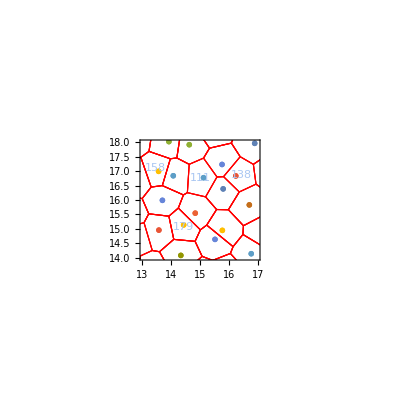

```mathematica
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{13,17},{14,18}},Frame->True]
```

```mathematica
polygon=Polygon[polygons[[534]][[1]]];
polygons[[873]][[1]]
```

{{15.0133,14.9654},{15.2322,15.1304},{15.575,15.6704},{15.1944,16.108},{14.5624,16.2554},{14.4263,16.1754},{14.2485,15.7208}}

```mathematica
cellIndex
```

```mathematica
p[[477]]
```

{-1.56207,7.90973}

```mathematica
strainfor={{1,0.00001},{0,1}};
strainback={{1,-0.00001},{0,1}};
```

```mathematica
strainfor.#&/@polygons[[534]][[1]]
```

{{15.9994,15.6624},{16.3778,16.2789},{15.8332,16.8101},{15.6051,16.7997},{15.2105,16.108},{15.5907,15.6704}}

```mathematica
(*This is system sheard by dgamma=0.001*)
```

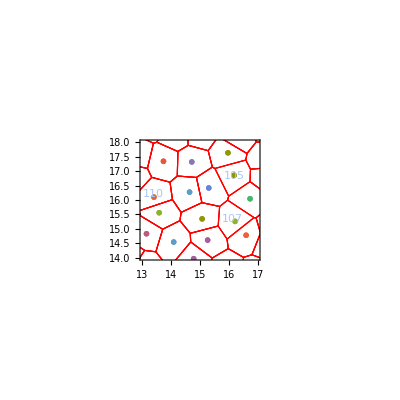

```mathematica
p0=strainfor.#&/@p;
vm0=VoronoiMesh[p0,{{min,max},{min,max}}];
dl0=ListPlot[Table[{p0[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm0,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl0,PlotRange->{{13,17},{14,18}},Frame->True]
```

```mathematica
(*This is system sheard by dgamma=-0.001*)
```

```mathematica
centroids0=RegionCentroid/@MeshPrimitives[vm0,2];
cellIndex0=Table[Nearest[centroids0->Automatic,p[[i]]][[1]],{i,1,Length[p]}];
```

```mathematica
Vareas0=PropertyValue[{vm0,2},MeshCellMeasure];
Vperis0=RegionMeasure/@(MeshPrimitives[vm0,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

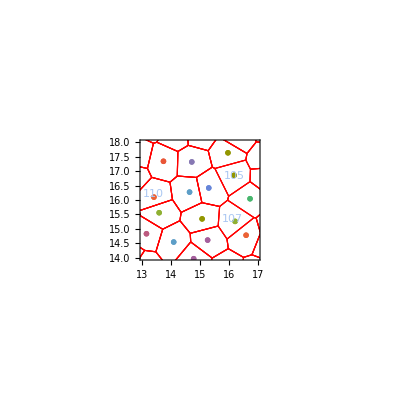

```mathematica
p1=strainback.#&/@p;
vm1=VoronoiMesh[p1,{{min+0.001*min,max+0.001*max},{min,max}}];
dl1=ListPlot[Table[{p1[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm1,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl1,PlotRange->{{13,17},{14,18}},Frame->True]
```

```mathematica
Vareas1=PropertyValue[{vm1,2},MeshCellMeasure];
Vperis1=RegionMeasure/@(MeshPrimitives[vm1,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

```mathematica
centroids1=RegionCentroid/@MeshPrimitives[vm1,2];
cellIndex1=Table[Nearest[centroids1->Automatic,p[[i]]][[1]],{i,1,Length[p]}];
```

```mathematica
(*This gives the numerical derivative of d2e/dgdg*)
numdericalCelli[i_,cellIndex_,cellIndex0_,cellIndex1_,ddx_,ka_,kp_,pa_,pp_]:=Module[{},
(ka(Vareas0[[cellIndex0[[i]]]]-pa)^2+kp(Vperis0[[cellIndex0[[i]]]]-pp)^2+ka(Vareas1[[cellIndex1[[i]]]]-pa)^2+kp(Vperis1[[cellIndex1[[i]]]]-pp)^2-2*(ka(VareasI[[cellIndex[[i]]]]-pa)^2+kp(VperisI[[cellIndex[[i]]]]-pp)^2))/ddx/ddx
]
(ka(Vareas0[[111]]-pa)^2+kp(Vperis0[[111]]-pp)^2+ka(Vareas1[[111]]-pa)^2+kp(Vperis1[[111]]-pp)^2-2*(ka(VareasI[[111]]-pa)^2+kp(VperisI[[111]]-pp)^2))/0.001/0.001
```

-0.732626

```mathematica
numdericalCelli[466,cellIndex,cellIndex0,cellIndex1,0.001,ka,kp,pa,pp]
```

-1.0784

```mathematica
(ka(Vareas0[[533]]-pa)^2+kp(Vperis0[[533]]-pp)^2+ka(Vareas1[[534]]-pa)^2+kp(Vperis1[[534]]-pp)^2-2*(ka(VareasI[[534]]-pa)^2+kp(VperisI[[534]]-pp)^2))/0.001/0.001
```

-1.0784

```mathematica
(ka(Vareas0[[873]]-pa)^2+kp(Vperis0[[873]]-pp)^2+ka(Vareas1[[873]]-pa)^2+kp(Vperis1[[873]]-pp)^2-2*(ka(VareasI[[873]]-pa)^2+kp(VperisI[[873]]-pp)^2))/0.001/0.001
```

0.0140697

```mathematica
polygons[[111]][[1]]
```

{{15.5883,16.7997},{15.1223,17.4517},{14.6256,17.2371},{14.5624,16.2554},{15.1944,16.108}}

```mathematica
(*neighbor list for the cell 534*)
neighborlist534={548,816,521,792,382,349};
(*neighbor list for the cell 111*)
neighborlist111={466,792,198,322,349};
(*neighbor list for the cell 873*)
neighborlist873={713,477,548,466,382,322,297};
```

```mathematica
Vareas=AnnotationValue[{vm,2},MeshCellMeasure];
Vperis=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
Vneighs=Length@@@cells;
```

```mathematica
Cross2d[r1_,r2_]:=r1[[1]]r2[[2]]-r1[[2]]r2[[1]]
voro[ri_,rj_,rk_]:=Module[{rij,rjk,rik,cross,d,α,β,γ},
rij=ri-rj;
rjk=rj-rk;
rik=ri-rk;

cross=Cross2d[rij,rjk];
d=2*cross*cross;

α=(rjk.rjk)*(rij.rik)/d;
β=-(rik.rik)*(rij.rjk)/d;
γ=(rij.rij)*(rik.rjk)/d;

α*ri+β*rj+γ*rk
];
```

```mathematica
ri={rix,riy}
rj={rjx,rjy}
rk={rkx,rky}
```

{rix,riy}

{rjx,rjy}

{rkx,rky}

```mathematica
hijk=voro[ri,rj,rk];
den=(rjx*rky-rjy*rkx)^3;
```

```mathematica
(*Analytical dirivatives of dhdr and dhdr*)
```

```mathematica
v1dri[r1_,r2_,r3_]:=(({{D[hijk[[1]],rix], D[hijk[[1]],riy]}, {D[hijk[[2]],rix], D[hijk[[2]],riy]}}))/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]}
```

```mathematica
v2drirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
v2driri[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rix],D[D[hijk[[2]],rix],rix]},
{D[D[hijk[[1]],riy],rix],D[D[hijk[[2]],riy],rix]}},
{{D[D[hijk[[1]],rix],riy],D[D[hijk[[2]],rix],riy]},
{D[D[hijk[[1]],riy],riy],D[D[hijk[[2]],riy],riy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
(*Analytical dirivatives of dhdg and d2hdgdg*)
```

```mathematica
dridg={riy,0};
drjdg={rjy,0};
drkdg={rky,0};
(*dh2dgdg[r1_,r2_,r3_]:=(v2drirj[r1,r2,r3].{r2[[2]],0}).{r1[[2]],0}+(v2drirj[r1,r3,r2].{r3[[2]],0}).{r1[[2]],0}+(v2driri[r1,r2,r3].{r1[[2]],0}).{r1[[2]],0}+(v2drirj[r2,r1,r3].{r1[[2]],0}).{r2[[2]],0}+(v2drirj[r2,r3,r1].{r3[[2]],0}).{r2[[2]],0}+(v2driri[r2,r1,r3].{r2[[2]],0}).{r2[[2]],0}+(v2drirj[r3,r1,r2].{r1[[2]],0}).{r3[[2]],0}+(v2drirj[r3,r2,r1].{r2[[2]],0}).{r3[[2]],0}+(v2driri[r3,r1,r2].{r3[[2]],0}).{r3[[2]],0};*)
dh2dgdg[r1_,r2_,r3_]:={(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]};
```

```mathematica
dhdg[r1_,r2_,r3_]:=(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0});
```

```mathematica
originalh=voro[p[[816]],p[[521]],p[[466]]]
dh2dgdg[p[[816]],p[[521]],p[[466]]]
dhdg[p[[816]],p[[521]],p[[466]]]
```

{16.3615,16.2789}

{0.385362,0.433415}

{16.2053,0.0545848}

```mathematica
v2drirj[p[[792]],p[[466]],p[[521]]]
```

v2drirk[{15.7644,17.232},{16.2407,16.8343},{15.8032,16.3853}]

{{{0.0773484,0.0586187},{-0.481907,-0.618014}},{{0.444112,-0.563314},{1.09184,-0.00413408}}}

```mathematica
strainfor={{1,0.001},{0,1}};
strainback={{1,-0.001},{0,1}};
```

```mathematica
(*This verifies dhdg and dh2dgdg*)
hForward=voro[strainfor.p[[816]],strainfor.p[[521]],strainfor.p[[466]]]
hback=voro[strainback.p[[816]],strainback.p[[521]],strainback.p[[466]]]
(hback+hForward-2*originalh)/0.001^2
-(hback-hForward)/0.002
```

{16.3777,16.279}

{16.3453,16.2789}

{0.385362,0.433415}

{16.2053,0.0545846}

```mathematica
Total[{16.20533371806765,0.05458459342477795}]
```

16.2599

```mathematica
Simplify[({{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}.{xx,yy}).{xxx,yyy}]
```

{a111 xx xxx+a121 xxx yy+a211 xx yyy+a221 yy yyy,a112 xx xxx+a122 xxx yy+a212 xx yyy+a222 yy yyy}

```mathematica
Simplify[(Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}].{xx,yy}).{xxx,yyy}]
```

{a111 xx xxx+a121 xxx yy+a112 xx yyy+a122 yy yyy,a211 xx xxx+a221 xxx yy+a212 xx yyy+a222 yy yyy}

```mathematica
Simplify[(Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}].{xxx,yyy}).{xx,yy}]
```

{a111 xx xxx+a112 xxx yy+a121 xx yyy+a122 yy yyy,a211 xx xxx+a212 xxx yy+a221 xx yyy+a222 yy yyy}

```mathematica
Simplify[({{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}.{xx,yy})]
```

{{a111 xx+a121 yy,a211 xx+a221 yy},{a112 xx+a122 yy,a212 xx+a222 yy}}

```mathematica
Transpose[{{{a111,a121},{a211,a221}},{{a112,a122},{a212,a222}}}][[2,1,1]]//MatrixForm
```

```mathematica
Transpose[{{a11,a12},{a21,a22}}].{b1,b2}.{c1,c2}
{{a11,a12},{a21,a22}}.{c1,c2}.{b1,b2}
```

(a11 b1+a21 b2) c1+(a12 b1+a22 b2) c2

```mathematica
RotateLeft[{1,2,3,4},1]
```

{2,3,4,1}

```mathematica
(*dedh,de2dhdh*)
perimetii[hc_,hm_]:=Sqrt[(hc-hm).(hc-hm)];
areaiWithri[hc_,hm_,ri_]:=0.5*Cross2d[hm-ri,hc-ri];
eWithri[{h1_,h2_,h3_,h4_,h5_},ri_]:=(areaiWithri[h1,h5,ri]+areaiWithri[h2,h1,ri]+areaiWithri[h3,h2,ri]+areaiWithri[h4,h3,ri]+areaiWithri[h5,h4,ri]-1)^2+(perimetii[h1,h2]+perimetii[h2,h3]+perimetii[h3,h4]+perimetii[h4,h5]+perimetii[h5,h1]-4)^2
```

```mathematica
areai[hc_,hm_]:=0.5*Cross2d[hm,hc];
(*PA is preferred area, and PP is preffer primeter*)
e[{h1_,h2_,h3_,h4_,h5_,h6_},KA_,KP_,PA_,PP_]:=KA(areai[h1,h6]+areai[h2,h1]+areai[h3,h2]+areai[h4,h3]+areai[h5,h4]+areai[h6,h5]-PA)^2+KP(perimetii[h1,h2]+perimetii[h2,h3]+perimetii[h3,h4]+perimetii[h4,h5]+perimetii[h5,h6]+perimetii[h6,h1]-PP)^2
```

```mathematica
Cross2d[polygons[[138]][[1]][[5]],polygons[[138]][[1]][[1]]]
```

-5.00948

```mathematica
p[[521]]
```

{16.2407,16.8343}

```mathematica
e[polygons[[534]][[1]]]
eWithri[polygons[[138]][[1]],p[[521]]]
```

0.2756

0.255696

```mathematica
0.6809844951448113
```

0.680984

```mathematica
polygon=Polygon[polygons[[534]][[1]]];
Vareas=Area[polygon];
Vperis=Perimeter[polygon];
(Vperis-4)^2+(Vareas-1)^2
```

0.2756

```mathematica
h1={h1x,h1y};h2={h2x,h2y};h3={h3x,h3y};h4={h4x,h4y};h5={h5x,h5y};h6={h6x,h6y};
Simplify[D[D[e[{h1,h2,h3,h4,h5,h6},KA,KP,PA,PP],h1x],h1x]]
```

2 ((0.5 h2y-0.5 h6y)^2 KA+((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2)))^2 KP+(-(h1x-h2x)^2/(((h1x-h2x)^2+(h1y-h2y)^2)^(3/2))+1/(√((h1x-h2x)^2+(h1y-h2y)^2))-(h1x-h6x)^2/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2))+1/(√((h1x-h6x)^2+(h1y-h6y)^2))) KP (√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2)-PP))

```mathematica
(*Analytical derivatives of dedh and d2edhdh*)
```

```mathematica
ei123456=e[{h1,h2,h3,h4,h5,h6},KA,KP,PA,PP];
dedh1[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={D[ei123456,h1x],D[ei123456,h1y]}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h1[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h1x],D[D[ei123456,h1x],h1y]},
{D[D[ei123456,h1x],h1y],D[D[ei123456,h1y],h1y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h2[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h2x],D[D[ei123456,h1x],h2y]},
{D[D[ei123456,h1y],h2x],D[D[ei123456,h1y],h2y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h6[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h6x],D[D[ei123456,h1x],h6y]},
{D[D[ei123456,h1y],h6x],D[D[ei123456,h1y],h6y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h3[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h3x],D[D[ei123456,h1x],h3y]},
{D[D[ei123456,h1y],h3x],D[D[ei123456,h1y],h3y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h4[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h4x],D[D[ei123456,h1x],h4y]},
{D[D[ei123456,h1y],h4x],D[D[ei123456,h1y],h4y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
e2dh1h5[{h1_,h2_,h3_,h4_,h5_,h6_}, ka_,kp_,pa_,pp_]:={{D[D[ei123456,h1x],h5x],D[D[ei123456,h1x],h5y]},
{D[D[ei123456,h1y],h5x],D[D[ei123456,h1y],h5y]}}/.{h1x->h1[[1]],h1y->h1[[2]],h2x->h2[[1]],h2y->h2[[2]],h3x->h3[[1]],h3y->h3[[2]],h4x->h4[[1]],h4y->h4[[2]],h5x->h5[[1]],h5y->h5[[2]],h6x->h6[[1]],h6y->h6[[2]],KA->ka,KP->kp,PA->pa,PP->pp};
```

```mathematica
(*This is to numerically test dedh and d2edrdr*)
```

```mathematica
e1x[vetice_,alpha_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v0=KP(Vperis-PP)^2+KA(Vareas-PA)^2;
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v1=KP(Vperis-PP)^2+KA(Vareas-PA)^2;
(v0-v1)/2/dx
]
e1y[vetice_,alpha_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v0=KP(Vperis-PP)^2+KA(Vareas-PA)^2;
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v1=KP(Vperis-PP)^2+KA(Vareas-PA)^2;
(v0-v1)/2/dx
]
e22xx[vetice_,alpha_,beta_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22yy[vetice_,alpha_,beta_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22xy[vetice_,alpha_,beta_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={dx,0};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={-dx,0};
p2[[beta]]+={0,-dx};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
e22yx[vetice_,alpha_,beta_,dx_,KA_,KP_,PA_,PP_]:=Module[{p2,poly2},
p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v11=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,dx};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v10=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v01=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

p2=polygons[[vetice]][[1]];
p2[[alpha]]+={0,-dx};
p2[[beta]]+={-dx,0};
poly2=Polygon[p2];
Vareas=Area[poly2];
Vperis=Perimeter[poly2];
v00=KP(Vperis-PP)^2+KA(Vareas-PA)^2;

(v11+v00-v01-v10)/(4 dx^2)
]
```

```mathematica
a=1;
ddx=10^-5.;
cellindex=534;
ka=0.5;
kp=0.7;
pa=1;
pp=4;
{e1x[cellindex,a,ddx,ka,kp,pa,pp],e1y[cellindex,a,ddx,ka,kp,pa,pp]}
dedh1[polygons[[534]][[1]],ka,kp,pa,pp]
dedh[polygons[[534]][[1]],ka,kp,pa,pp]
```

{-0.381999,0.673454}

{-0.381999,0.673454}

dedh[{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}},0.5,0.7,1,4]

```mathematica
a=1;
b=1;
ddx=10^-5.;
cellindex=534;
ka=0.5;
kp=0.7;
pa=1;
pp=4;
({{e22xx[cellindex,a,b,ddx,ka,kp,pa,pp], e22xy[cellindex,a,b,ddx,ka,kp,pa,pp]}, {e22yx[cellindex,a,b,ddx,ka,kp,pa,pp], e22yy[cellindex,a,b,ddx,ka,kp,pa,pp]}})//MatrixForm
```

(-0.296709 | -0.303007
-0.303007 | -0.766742)

```mathematica
(*Now we verify the analytical expression for de2dhdh*)
```

```mathematica
e2dh1h1[polygons[[534]][[1]],ka,kp,pa,pp]//MatrixForm
```

(-0.296703 | -0.303007
-0.303007 | -0.766747)

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],0],1,1,1,4]//MatrixForm
```

(0.15844 KA+0.269956 KP | 0.235273 KA+0.709992 KP
-0.20476 KA-0.493322 KP | -0.304055 KA-1.29745 KP)

```mathematica
a=1;
b=2;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h2[polygons[[534]][[1]]]//MatrixForm
```

(2.54278 | -0.571918
-3.08061 | 0.0436101)

(2.54278 | -0.571891
-3.08062 | 0.0436102)

```mathematica
de2dhihjxx[polygons[[534]][[1]],4](*45 are wrong*)
```

-0.371523

```mathematica
a=1;
b=3;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h3[polygons[[534]][[1]]]//MatrixForm
```

(0.428396 | 0.945265
-0.698082 | -1.60151)

(0.428396 | 0.945265
-0.698082 | -1.60151)

```mathematica
a=1;
b=4;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h4[polygons[[534]][[1]]]//MatrixForm
```

(-0.694974 | 0.975266
1.15569 | -1.68096)

(-0.694974 | 0.975266
1.15569 | -1.68096)

```mathematica
a=1;
b=5;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h5[polygons[[534]][[1]]]//MatrixForm
```

(-1.44267 | -0.105313
2.45251 | 0.194607)

(-1.44267 | -0.105315
2.45251 | 0.194607)

```mathematica
a=1;
b=6;
ddx=10^-5.;
cellindex=534;
({{e22xx[cellindex,a,b,ddx], e22xy[cellindex,a,b,ddx]}, {e22yx[cellindex,a,b,ddx], e22yy[cellindex,a,b,ddx]}})//MatrixForm
e2dh1h6[polygons[[534]][[1]]]//MatrixForm
```

(-0.462576 | -0.742086
0.67174 | 4.05124)

(-0.462577 | -0.742088
0.671732 | 4.05124)

```mathematica
RotateLeft[{a1,a2,a3,a4,a5,a6},1]
```

{a2,a3,a4,a5,a6,a1}

```mathematica
(*This is the analytical de2dgdg*)
(*de2dgdge[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Table[e2dh1h1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]]+e2dh1h2[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[2+i,6]]]]],p[[neilist[[Mod[3+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,1]]]]]]+e2dh1h6[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[Mod[6+i,6]]]]],p[[neilist[[Mod[1+i,6]]]]]].dhdg[ri,p[[neilist[[Mod[1+i,6]]]]],p[[neilist[[Mod[2+i,6]]]]]]+dedh1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dh2dgdg[RotateLeft[{h1,h2,h3,h4,h5,h6},i]],{i,0,5}]*)
de2dgdge[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Sum[e2dh1h1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h2[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]],p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+
e2dh1h3[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]],p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h4[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]],p[[neilist[[If[5+i==6,6,Mod[5+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+
e2dh1h5[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[5+i==6,6,Mod[5+i,6]]]]]],p[[neilist[[If[6+i==6,6,Mod[6+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+e2dh1h6[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[6+i==6,6,Mod[6+i,6]]]]]],p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]]+dedh1[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dh2dgdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]],{i,0,5}]
```

```mathematica
de2dgdgeTest[{h1_,h2_,h3_,h4_,h5_,h6_},ri_,neilist_]:=Sum[e2dh1h3[RotateLeft[{h1,h2,h3,h4,h5,h6},i]].dhdg[ri,p[[neilist[[If[3+i==6,6,Mod[3+i,6]]]]]],p[[neilist[[If[4+i==6,6,Mod[4+i,6]]]]]]].dhdg[ri,p[[neilist[[If[1+i==6,6,Mod[1+i,6]]]]]],p[[neilist[[If[2+i==6,6,Mod[2+i,6]]]]]]],{i,1,1}]
```

```mathematica
de2dgdge[polygons[[534]][[1]],p[[466]],neighborlist]
```

-1.54469

```mathematica
(*Now we verified the analytical d2edgdg matches the numerical result from the beginning of this notebook!*)
```

3

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],0]].dhdg[p[[466]],p[[neighborlist[[3]]]],p[[neighborlist[[4]]]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

116.065

```mathematica
e2dh1h3[RotateLeft[polygons[[534]][[1]],1]].dhdg[p[[466]],p[[neighborlist[[4]]]],p[[neighborlist[[5]]]]].dhdg[p[[466]],p[[neighborlist[[2]]]],p[[neighborlist[[3]]]]]
```

-441.342

```mathematica
dh2dgdg[polygons[[534]][[1]]]
```

dh2dgdg[{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}}]

```mathematica
e2dh1h1[polygons[[534]][[1]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]].dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

-89.7364

```mathematica
e2dh1h1[polygons[[534]][[1]]]
dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
dhdg[p[[466]],p[[neighborlist[[1]]]],p[[neighborlist[[2]]]]]
```

{{-0.370958,-0.501238},{-0.501238,-1.00699}}

{15.8193,-0.197706}

{15.8193,-0.197706}

```mathematica
p[[466]];
Mod[7,6]
```

1

```mathematica
Simplify[D[D[ei123456,h1x],h1x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h6x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hjx,h6y->hjy,h5x->hjLastx,h5y->hjLasty}
```

2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)+√((h4x-hjLastx)^2+(h4y-hjLasty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((hjLastx-hjx)^2+(hjLasty-hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h2x]]/.{h1x->hix,h1y->hiy,h2x->hjx,h2y->hjy,h6x->hiLastx,h6y->hiLasty,h3x->hjNextx,h3y->hjNexty}
```

2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-h4x+hjNextx)^2+(-h4y+hjNexty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h4x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h3x->hjLastx,h3y->hjLasty,h4x->hjx,h4y->hjy,h6x->hiLastx,h6y->hiLasty,h5x->hjNextx,h5y->hjNexty}
```

2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP

## Analytical function in Mathematica

```mathematica
hv={h1,h2,h2,h3,h4,h5,h6}
```

{{h1x,h1y},{h2x,h2y},{h2x,h2y},{h3x,h3y},{h4x,h4y},{h5x,h5y},{h6x,h6y}}

```mathematica
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];

area[hv_List]:=Sum[0.5*Cross2d[hv[[i]],hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]],{i,1,Length[hv]}];
```

```mathematica
peri[hv_List]:=Sum[Sqrt[(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]]).(hv[[i]]-hv[[If[1+i==Length[hv],Length[hv],Mod[1+i,Length[hv]]]]])],{i,1,Length[hv]}];
peri[{{1,2},{-1,2},{-1,-2},{1,-2}}]
```

12

```mathematica
Simplify[D[ei123456,h1x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

0.5 (-1. hiLasty+1. hiNexty) KA (-1. h3y h4x+1. h3x h4y-1. h4y h5x+1. h4x h5y-1. h5y hiLastx+1. h5x hiLasty+1. h3y hiNextx-1. h3x hiNexty-1. hiLasty hix+1. hiNexty hix+1. hiLastx hiy-1. hiNextx hiy-2. PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP)

```mathematica
Simplify[D[ei123456,h1y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

0.5 (-1. hiLastx+1. hiNextx) KA (1. h3y h4x-1. h3x h4y+1. h4y h5x-1. h4x h5y+1. h5y hiLastx-1. h5x hiLasty-1. h3y hiNextx+1. h3x hiNexty+1. hiLasty hix-1. hiNexty hix-1. hiLastx hiy+1. hiNextx hiy+2. PA)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP)

```mathematica
(*This is the 1st derivative of e w.r.t. h*)
```

```mathematica
dedhGeneral[hv_List,KA_,KP_,PA_,PP_]:=Module[{dedhx,dedhy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
dedhx=(-1. hiLasty+1. hiNexty) KA (a-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
dedhy=(-1. hiLastx+1. hiNextx) KA (PA-a)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP);
{dedhx,dedhy}
]
```

```mathematica
CForm[(-1. hiLasty+1. hiNexty) KA (A-PA)+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (P-PP) //.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

(-1.*hiLasty + 1.*hiNexty)*KA*(A - PA) + 2*KP*(P - PP)*((-hiLastx + hix)/
       Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNextx + hix)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))

```mathematica
CForm[(-1. hiLastx+1. hiNextx) KA (PA-A)+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (P-PP)//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

(-1.*hiLastx + 1.*hiNextx)*KA*(-A + PA) + 
   2*KP*(P - PP)*((-hiLasty + hiy)/
       Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNexty + hiy)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy))
      )

```mathematica
(*This gives the analytical formula for each terms for de2dhidhj*)
Simplify[D[D[ei123456,h1x],h1x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h2x]]/.{h1x->hix,h1y->hiy,h2x->hjx,h2y->hjy,h6x->hiLastx,h6y->hiLasty,h3x->hjNextx,h3y->hjNexty}
```

2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-h4x+hjNextx)^2+(-h4y+hjNexty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h6x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hjx,h6y->hjy,h5x->hjLastx,h5y->hjLasty}
```

2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)+√((h4x-hjLastx)^2+(h4y-hjLasty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((hjLastx-hjx)^2+(hjLasty-hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h4x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h3x->hjLastx,h3y->hjLasty,h4x->hjx,h4y->hjy,h6x->hiLastx,h6y->hiLasty,h5x->hjNextx,h5y->hjNexty}
```

2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP

```mathematica
(*This is the generalized function for de2dhidhj*)

de2dhihjxx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xx=2 ((-0.5 hiLasty+0.5 hiNexty)^2 KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLastx+hix)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNextx+hix)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2xx=2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[j==Length[hv],
de2xx=2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2xx=2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xx
];
```

```mathematica
CForm[2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x],x_^1.5:>HoldForm[Sqrt[x]*Sqrt[x]*Sqrt[x]]}]
```

2*(-0.5*hiLasty + 0.5*hiNexty)*(-0.5*hjLasty + 0.5*hjNexty)*KA + 
   2*KP*((-hiLastx + hix)/Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNextx + hix)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))*
    ((-hjLastx + hjx)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy)) + 
      (-hjNextx + hjx)/Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy)))

```mathematica
CForm[2 ((-0.5 hiy+0.5 hjNexty) (-0.5 hiLasty+0.5 hjy) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (P-PP))//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*((-0.5*hiy + 0.5*hjNexty)*(-0.5*hiLasty + 0.5*hjy)*KA - 
     (KP*(P - PP)*((hiy - hjy)*(hiy - hjy)))/
      Power((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy),1.5) + 
     KP*((-hiLastx + hix)/
         Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
        (hix - hjx)/Sqrt((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy)))*
      ((-hix + hjx)/Sqrt((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy)) + 
        (-hjNextx + hjx)/
         Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy))))

```mathematica
CForm[2 ((0.5 hiy-0.5 hjLasty) (0.5 hiNexty-0.5 hjy) KA+((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hiy-hjy)^2 KP (P-PP))//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*((0.5*hiy - 0.5*hjLasty)*(0.5*hiNexty - 0.5*hjy)*KA - (KP*(P - PP)*((hiy - hjy)*(hiy - hjy)))/
      Power((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy),1.5) + 
     KP*((-hiNextx + hix)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)) + 
        (hix - hjx)/Sqrt((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy)))*
      ((-hix + hjx)/Sqrt((hix - hjx)*(hix - hjx) + (hiy - hjy)*(hiy - hjy)) + 
        (-hjLastx + hjx)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy))))

```mathematica
CForm[2 (-0.5 hiLasty+0.5 hiNexty) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*(-0.5*hiLasty + 0.5*hiNexty)*(-0.5*hjLasty + 0.5*hjNexty)*KA + 
   2*KP*((-hiLastx + hix)/Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNextx + hix)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))*
    ((-hjLastx + hjx)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy)) + 
      (-hjNextx + hjx)/Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy)))

```mathematica
Simplify[D[D[ei123456,h1x],h1y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1x],h2y]]/.{h1x->hix,h1y->hiy,h2x->hjx,h2y->hjy,h6x->hiLastx,h6y->hiLasty,h3x->hjNextx,h3y->hjNexty}
```

2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-0.5 KA (1. h4y h5x-1. h4x h5y+1. h5y hiLastx-1. h5x hiLasty+1. hiLasty hix-1. hiLastx hiy-1. h4y hjNextx+1. h4x hjNexty+1. hiy hjx-1. hjNexty hjx-1. hix hjy+1. hjNextx hjy+2. PA)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-h4x+hjNextx)^2+(-h4y+hjNexty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2)-PP)

```mathematica
Simplify[D[D[ei123456,h1x],h6y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hjx,h6y->hjy,h5x->hjLastx,h5y->hjLasty}
```

2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+0.5 KA (1. h3y h4x-1. h3x h4y-1. h3y hiNextx+1. h3x hiNexty-1. hiNexty hix+1. hiNextx hiy+1. h4y hjLastx-1. h4x hjLasty-1. hiy hjx+1. hjLasty hjx+1. hix hjy-1. hjLastx hjy+2. PA)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)+√((h4x-hjLastx)^2+(h4y-hjLasty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((hjLastx-hjx)^2+(hjLasty-hjy)^2)-PP)

```mathematica
Simplify[D[D[ei123456,h1x],h4y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h3x->hjLastx,h3y->hjLasty,h4x->hjx,h4y->hjy,h6x->hiLastx,h6y->hiLasty,h5x->hjNextx,h5y->hjNexty}
```

2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP

```mathematica
de2dhihjxy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2xy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2xy=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2xy=2 (0.5 hix-0.5 hjNextx) (-0.5 hiLasty+0.5 hjy) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP- KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2xy=2 (-0.5 hix+0.5 hjLastx) (0.5 hiNexty-0.5 hjy) KA+2 ((-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hix-hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP+KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2xy=2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2xy
];
```

```mathematica
CForm[2 (-0.5 hiLasty+0.5 hiNexty) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*(-0.5*hiLasty + 0.5*hiNexty)*(0.5*hjLastx - 0.5*hjNextx)*KA + 
   2*KP*((-hiLastx + hix)/Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNextx + hix)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))*
    ((-hjLasty + hjy)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy)) + 
      (-hjNexty + hjy)/Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy)))

```mathematica
Simplify[D[D[ei123456,h1y],h1x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1y],h2x]]/.{h1x->hix,h1y->hiy,h2x->hjx,h2y->hjy,h6x->hiLastx,h6y->hiLasty,h3x->hjNextx,h3y->hjNexty}
```

2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+0.5 KA (1. h4y h5x-1. h4x h5y+1. h5y hiLastx-1. h5x hiLasty+1. hiLasty hix-1. hiLastx hiy-1. h4y hjNextx+1. h4x hjNexty+1. hiy hjx-1. hjNexty hjx-1. hix hjy+1. hjNextx hjy+2. PA)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-h4x+hjNextx)^2+(-h4y+hjNexty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2)-PP)

```mathematica
Simplify[D[D[ei123456,h1y],h6x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hjx,h6y->hjy,h5x->hjLastx,h5y->hjLasty}
```

2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-0.5 KA (1. h3y h4x-1. h3x h4y-1. h3y hiNextx+1. h3x hiNexty-1. hiNexty hix+1. hiNextx hiy+1. h4y hjLastx-1. h4x hjLasty-1. hiy hjx+1. hjLasty hjx+1. hix hjy-1. hjLastx hjy+2. PA)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)+√((h4x-hjLastx)^2+(h4y-hjLasty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((hjLastx-hjx)^2+(hjLasty-hjy)^2)-PP)

```mathematica
Simplify[D[D[ei123456,h1y],h4x]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h3x->hjLastx,h3y->hjLasty,h4x->hjx,h4y->hjy,h6x->hiLastx,h6y->hiLasty,h5x->hjNextx,h5y->hjNexty}
```

2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP

```mathematica
de2dhihjyx[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yx,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yx=2 ((0.5 hiLastx-0.5 hiNextx) (-0.5 hiLasty+0.5 hiNexty) KA+((-hiLastx+hix)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNextx+hix)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP+(-((-hiLastx+hix) (-hiLasty+hiy))/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))-((-hiNextx+hix) (-hiNexty+hiy))/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))) KP (p-PP))];
If[j==2,

de2yx=2 (-0.5 hiy+0.5 hjNexty) (0.5 hiLastx-0.5 hjx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP+ KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[j==Length[hv],
de2yx=2 (0.5 hiy-0.5 hjLasty) (-0.5 hiNextx+0.5 hjx) KA+2 ((-hix+hjx)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) ((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) KP-KA (PA-a)+1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))2 (hix-hjx) (hiy-hjy) KP (p-PP)];
If[!(j==1||j==2||j==Length[hv]),

de2yx=2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yx
];
```

```mathematica
CForm[2 (0.5 hiLastx-0.5 hiNextx) (-0.5 hjLasty+0.5 hjNexty) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLastx+hjx)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNextx+hjx)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*(0.5*hiLastx - 0.5*hiNextx)*(-0.5*hjLasty + 0.5*hjNexty)*KA + 
   2*KP*((-hiLasty + hiy)/Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNexty + hiy)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))*
    ((-hjLastx + hjx)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy)) + 
      (-hjNextx + hjx)/Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy)))

```mathematica
Simplify[D[D[ei123456,h1y],h1y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hiLastx,h6y->hiLasty}
```

2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1y],h2y]]/.{h1x->hix,h1y->hiy,h2x->hjx,h2y->hjy,h6x->hiLastx,h6y->hiLasty,h3x->hjNextx,h3y->hjNexty}
```

2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (√((h4x-h5x)^2+(h4y-h5y)^2)+√((h5x-hiLastx)^2+(h5y-hiLasty)^2)+√((-hiLastx+hix)^2+(-hiLasty+hiy)^2)+√((-h4x+hjNextx)^2+(-h4y+hjNexty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1y],h6y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h6x->hjx,h6y->hjy,h5x->hjLastx,h5y->hjLasty}
```

2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (√((h3x-h4x)^2+(h3y-h4y)^2)+√((-h3x+hiNextx)^2+(-h3y+hiNexty)^2)+√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)+√((h4x-hjLastx)^2+(h4y-hjLasty)^2)+√((hix-hjx)^2+(hiy-hjy)^2)+√((hjLastx-hjx)^2+(hjLasty-hjy)^2)-PP))

```mathematica
Simplify[D[D[ei123456,h1y],h4y]]/.{h1x->hix,h1y->hiy,h2x->hiNextx,h2y->hiNexty,h3x->hjLastx,h3y->hjLasty,h4x->hjx,h4y->hjy,h6x->hiLastx,h6y->hiLasty,h5x->hjNextx,h5y->hjNexty}
```

2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP

```mathematica
de2dhihjyy[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{de2yy,hix,hiy,hiLastx,hiLasty,hiNextx,hiNexty,hjx,hjy,hjLastx,hjLasty,hjNextx,hjNexty,p,a},
p=peri[hv];
a=area[hv];
hix=hv[[1]][[1]];hiy=hv[[1]][[2]];hiLastx=hv[[Length[hv]]][[1]];hiLasty=hv[[Length[hv]]][[2]];hiNextx=hv[[2]][[1]];hiNexty=hv[[2]][[2]];
hjx=hv[[j]][[1]];hjy=hv[[j]][[2]];hjLastx=hv[[If[j-1==0,Length[hv],j-1]]][[1]];hjLasty=hv[[If[j-1==0,Length[hv],j-1]]][[2]];hjNextx=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[1]];hjNexty=hv[[If[j+1==Length[hv],Length[hv],Mod[j+1,Length[hv]]]]][[2]];
(*if we are doing de2dhidhi*)
If[j==1,

de2yy=2 ((-0.5 hiLastx+0.5 hiNextx)^2 KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2)))^2 KP+(-(-hiLasty+hiy)^2/(((-hiLastx+hix)^2+(-hiLasty+hiy)^2)^(3/2))+1/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))-(-hiNexty+hiy)^2/(((-hiNextx+hix)^2+(-hiNexty+hiy)^2)^(3/2))+1/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) KP (p-PP))];
If[j==2,

de2yy=2 ((0.5 hix-0.5 hjNextx) (0.5 hiLastx-0.5 hjx) KA+((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[j==Length[hv],
de2yy=2 ((-0.5 hix+0.5 hjLastx) (-0.5 hiNextx+0.5 hjx) KA+((-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))+(hiy-hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))) ((-hiy+hjy)/(√((hix-hjx)^2+(hiy-hjy)^2))+(-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))) KP-1/(((hix-hjx)^2+(hiy-hjy)^2)^(3/2))(hix-hjx)^2 KP (p-PP))];
If[!(j==1||j==2||j==Length[hv]),

de2yy=2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP];
de2yy
];
```

```mathematica
CForm[2 (0.5 hiLastx-0.5 hiNextx) (0.5 hjLastx-0.5 hjNextx) KA+2 ((-hiLasty+hiy)/(√((-hiLastx+hix)^2+(-hiLasty+hiy)^2))+(-hiNexty+hiy)/(√((-hiNextx+hix)^2+(-hiNexty+hiy)^2))) ((-hjLasty+hjy)/(√((hjLastx-hjx)^2+(hjLasty-hjy)^2))+(-hjNexty+hjy)/(√((-hjNextx+hjx)^2+(-hjNexty+hjy)^2))) KP//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

2*(0.5*hiLastx - 0.5*hiNextx)*(0.5*hjLastx - 0.5*hjNextx)*KA + 
   2*KP*((-hiLasty + hiy)/Sqrt((-hiLastx + hix)*(-hiLastx + hix) + (-hiLasty + hiy)*(-hiLasty + hiy)) + 
      (-hiNexty + hiy)/Sqrt((-hiNextx + hix)*(-hiNextx + hix) + (-hiNexty + hiy)*(-hiNexty + hiy)))*
    ((-hjLasty + hjy)/Sqrt((hjLastx - hjx)*(hjLastx - hjx) + (hjLasty - hjy)*(hjLasty - hjy)) + 
      (-hjNexty + hjy)/Sqrt((-hjNextx + hjx)*(-hjNextx + hjx) + (-hjNexty + hjy)*(-hjNexty + hjy)))

```mathematica
(*All the functions above are tested correct!*)
```

```mathematica
de2dhihjyy[polygons[[873]][[1]],1,1.2,1.1,1,4]
```

Part::partd: Part specification 1.2⟦2⟧ is longer than depth of object.

1.2⟦2⟧

3.48625

```mathematica
a=1;
b=7;
ddx=10^-5.;
cellindex=873;
({{e22xx[cellindex,a,b,ddx,ka,kp,pa,pp], e22xy[cellindex,a,b,ddx,ka,kp,pa,pp]}, {e22yx[cellindex,a,b,ddx,ka,kp,pa,pp], e22yy[cellindex,a,b,ddx,ka,kp,pa,pp]}})//MatrixForm
de2dhdhGeneral[polygons[[873]][[1]],b,ka,kp,pa,pp]
```

(0.397379 | 0.198662
2.35571 | 0.651732)

{{0.397379,0.198662},{2.35571,0.651731}}

```mathematica
a=1;
ddx=10^-5.;
cellindex=873;
ka=0.5;
kp=0.7;
pa=1;
pp=4;
{e1x[cellindex,a,ddx,ka,kp,pa,pp],e1y[cellindex,a,ddx,ka,kp,pa,pp]}
dedhGeneral[polygons[[873]][[1]],ka,kp,pa,pp]
```

{0.0139085,0.244374}

{0.0139085,0.244374}

```mathematica
de2dhihjxx[polygons[[534]][[1]],2]
```

2.54278

```mathematica
de2dhdhGeneral[hv_List,j_,KA_,KP_,PA_,PP_]:=Module[{},
{{de2dhihjxx[hv,j,KA,KP,PA,PP],de2dhihjxy[hv,j,KA,KP,PA,PP]},{de2dhihjyx[hv,j,KA,KP,PA,PP],de2dhihjyy[hv,j,KA,KP,PA,PP]}}
]
```

```mathematica
(*This verifies de2dhdhGeneral*)
```

```mathematica
e2dh1h6[polygons[[534]][[1]],1.2,1.1,1,4]
de2dhdhGeneral[polygons[[534]][[1]],6,1.2,1.1,1,4]
```

{{-0.522393,-0.825193},{0.741307,4.4874}}

{{-0.522393,-0.825193},{0.741307,4.4874}}

```mathematica
(*These are the analytical forms for dhdgamma and d2hdgamma2*)
```

```mathematica
r1={r1x,r1y};r2={r2x,r2y};r3={r3x,r3y};
CForm[Simplify[dh2dgdg[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((r2y*(r2y - r3y)*r3y)/(-(r2y*r3x) + r2x*r3y),(2*r2y*(-r2x + r3x)*r3y - r3x*(r2y*r2y) + r2x*(r3y*r3y))/(-(r2y*r3x) + r2x*r3y))

```mathematica
CForm[Simplify[dhdg[r1,r2,r3]/.{r1x->0,r1y->0}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List((r2y*(r2x - r3x)*r3y)/(-(r2y*r3x) + r2x*r3y),(2*r2x*r3x*(-r2y + r3y) - r3y*(r2x*r2x) + r2y*(r3y*(-r2y + r3y) + r3x*r3x))/
    (-2*r2y*r3x + 2*r2x*r3y))

```mathematica
dhdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+r2y r3x^2-r2x^2 r3y-r2y^2 r3y+2 r2x r3x r3y+r2y r3y^2+r1x^2 (-r2y+r3y)+r1y^2 (-r2y+r3y)+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+r1y (r2x^2+r2y^2-r3x^2-r3y^2))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}
];
d2hdgdgGeneral[r1_List,r2_List,r3_List]:=Module[{r1x,r1y,r2x,r2y,r3x,r3y},
r1x=r1[[1]];r1y=r1[[2]];r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-r2y^2 r3x+r1y^2 (-r2x+r3x)-2 r2x r2y r3y+2 r2y r3x r3y+r2x r3y^2+r1x (r2y^2-r3y^2)+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y)))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}
];
```

```mathematica
dhdgGeneraliCenter[r2_List,r3_List]:=Module[{r2x,r2y,r3x,r3y},
r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r2y (r2x-r3x) r3y)/(-r2y r3x+r2x r3y),(-r2x^2 r3y+2 r2x r3x (-r2y+r3y)+r2y (r3x^2+r3y (-r2y+r3y)))/(-2 r2y r3x+2 r2x r3y)}
];
d2hdgdgGeneraliCenter[r2_List,r3_List]:=Module[{r2x,r2y,r3x,r3y},
r2x=r2[[1]];r2y=r2[[2]];r3x=r3[[1]];r3y=r3[[2]];
{(r2y (r2y-r3y) r3y)/(-r2y r3x+r2x r3y),(-r2y^2 r3x+2 r2y (-r2x+r3x) r3y+r2x r3y^2)/(-r2y r3x+r2x r3y)}
];
```

```mathematica
hForward=voro[strainfor.p[[816]],strainfor.p[[521]],strainfor.p[[466]]];
hback=voro[strainback.p[[816]],strainback.p[[521]],strainback.p[[466]]];
(hback+hForward-2*originalh)/0.001^2
-(hback-hForward)/0.002
```

{0.385362,0.433415}

{16.2053,0.0545846}

```mathematica
{{aa,bb},{cc,dd}}.dhdgGeneraliCenter[p[[521]]-p[[816]],p[[466]]-p[[816]]].dhdgGeneraliCenter[p[[521]]-p[[816]],p[[466]]-p[[816]]]
```

0.375506 (0.375506 aa+0.0545848 bb)+0.0545848 (0.375506 cc+0.0545848 dd)

```mathematica
{{aa,bb},{cc,dd}}.dhdgGeneral[p[[816]],p[[521]],p[[466]]].dhdgGeneral[p[[816]],p[[521]],p[[466]]]
```

16.2053 (16.2053 aa+0.0545848 bb)+0.0545848 (16.2053 cc+0.0545848 dd)

```mathematica
dhdgGeneral[p[[521]],p[[816]],p[[466]]]
d2hdgdgGeneral[p[[816]],p[[521]],p[[466]]]
```

{16.2053,0.0545848}

{0.385362,0.433415}

```mathematica
(*Now this is to calculate de2dgammadgamma for cell i*)
```

```mathematica
d2eidgdgGeneral[vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneral[ri,p[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]],p[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]].dhdgGeneral[ri,p[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],p[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneral[ri,p[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]],p[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]],{i,0,Length[vList]-1}]
]
```

```mathematica
(*d2eidgdgGeneral works*)
```

```mathematica
d2eidgdgGeneraliCenter[vList_List,ri_,neilist_List,KA_,KP_,PA_,PP_]:=Module[{},
Sum[Sum[de2dhdhGeneral[RotateLeft[vList,i],j,KA,KP,PA,PP].dhdgGeneraliCenter[p[[neilist[[If[j+i==Length[vList],Length[vList],Mod[j+i,Length[vList]]]]]]]-ri,p[[neilist[[If[j+1+i==Length[vList]||j+1+i==2*Length[vList],Length[vList],Mod[j+1+i,Length[vList]]]]]]]-ri].dhdgGeneraliCenter[p[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]]-ri,p[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]-ri],{j,1,Length[vList]}]+dedhGeneral[RotateLeft[vList,i],KA,KP,PA,PP].d2hdgdgGeneraliCenter[p[[neilist[[If[1+i==Length[vList],Length[vList],Mod[1+i,Length[vList]]]]]]]-ri,p[[neilist[[If[2+i==Length[vList],Length[vList],Mod[2+i,Length[vList]]]]]]]-ri],{i,0,Length[vList]-1}]
]
```

```mathematica
d2eidgdgGeneraliCenter[polygons[[534]][[1]],p[[466]],neighborlist534,ka,kp,pa,pp]
```

-1.0784

```mathematica
d2eidgdgGeneral[polygons[[111]][[1]],p[[382]],neighborlist111,ka,kp,pa,pp]
```

-0.732629

```mathematica
d2eidgdgGeneral[polygons[[873]][[1]],p[[349]],neighborlist873,ka,kp,pa,pp]
```

0.0140695

```mathematica
d2eidgdgGeneral[polygons[[534]][[1]],p[[466]],neighborlist534,ka,kp,pa,pp]
```

-1.0784

```mathematica
Length[polygons[[111]][[1]]]
```

5

```mathematica
(*Now we need to generate the neighbor list for cell i*)
(*Compute Delaunay triangulation*)
delaunayMesh=DelaunayMesh[p];

(*Find vertices of the Delaunay triangulation that form triangles with center'i'*)
trianglesWithCenterI=Select[First/@MeshCells[delaunayMesh,2],MemberQ[#,466]&];

(*Find neighboring centers*)
neighboringCenters=DeleteCases[Union[Flatten[trianglesWithCenterI]],466]
```

{349,382,521,548,792,816}

```mathematica
{548,816,521,792,382,349};
```

{}

```mathematica
reorderCCWIndices[centerIndex_,neighborIndices_List,allPoints_]:=Module[{center,neighbors,angles,sortedIndices},center=allPoints[[centerIndex]];
neighbors=allPoints[[neighborIndices]];
angles=ArcTan@@@(#-center&/@neighbors);
sortedIndices=Ordering[angles];
neighborIndices[[sortedIndices]]
(*Table[neighborIndices[[FirstPosition[sortedIndices,i][[1]]]],{i,1,Length[neighborIndices]}]*)]
```

```mathematica
testlist=reorderCCWIndices[466,neighboringCenters,p]
```

{349,548,816,521,792,382}

```mathematica
(*neighborListRightOrder takes in the index of cell center i and returns the neighbouring cell centers in the order that matches how the vertices of cell center i are stores. Cell center i is the center of cell cellIndex[[i]]*)
```

```mathematica
neighborListRightOrder[i_,voronoiPolygons_List,cellIndex_,allPoints_]:=Module[{trianglesWithCenteri,neighborListRandomOrder,neighborListCCWOrder,delaunay,vetices,firstVerticeID},
delaunay=DelaunayMesh[allPoints];
trianglesWithCenteri=Select[First/@MeshCells[delaunay,2],MemberQ[#,i]&];
neighborListRandomOrder=DeleteCases[Union[Flatten[trianglesWithCenteri]],i];
neighborListCCWOrder=reorderCCWIndices[i,neighborListRandomOrder,allPoints];
vetices=Table[voro[allPoints[[i]],allPoints[[neighborListCCWOrder[[j]]]],allPoints[[neighborListCCWOrder[[If[j+1==Length[neighborListCCWOrder],Length[neighborListCCWOrder],Mod[j+1,Length[neighborListCCWOrder]]]]]]]],{j,1,Length[neighborListCCWOrder]}];
firstVerticeID=Nearest[vetices->Automatic,polygons[[cellIndex[[i]]]][[1]][[1]]][[1]];
RotateLeft[neighborListCCWOrder,firstVerticeID-1]
]
```

```mathematica
test=Table[voro[p[[466]],p[[testlist[[j]]]],p[[testlist[[If[j+1==Length[testlist],Length[testlist],Mod[j+1,Length[testlist]]]]]]]],{j,1,Length[testlist]}]
```

{{15.575,15.6704},{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108}}

```mathematica
polygons[[534]][[1]]
```

{{15.9837,15.6624},{16.3615,16.2789},{15.8164,16.8101},{15.5883,16.7997},{15.1944,16.108},{15.575,15.6704}}

```mathematica
neighborListRightOrder[466,polygons,cellIndex,p]
```

{548,816,521,792,382,349}

```mathematica
polygons[[1]][[1]]
```

{{3.07948,23.2497},{3.90182,22.8497},{4.25872,23.6892},{3.48145,24.201}}

## Analytical function to evaluate the selected region in the system

```mathematica
(*Now we can build the function d2edgdg for the entire system*)
```

```mathematica
d2eidgdgEntire[allPoints_,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,centroids,cellIndex},
min=Min[allPoints]-.1;max=Max[allPoints]+.1;
vm=VoronoiMesh[allPoints,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
centroids=RegionCentroid/@MeshPrimitives[vm,2];
cellIndex=Table[Nearest[centroids->Automatic,allPoints[[i]]][[1]],{i,1,Length[allPoints]}];
Sum[d2eidgdgGeneraliCenter[voronoiPolygons[[cellIndex[[i]]]][[1]],allPoints[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPoints],KA,KP,PA,PP],{i,pointID}]
]
```

```mathematica
d2eidgdgEach[allPoints_,pointID_List,KA_,KP_,PA_,PP_]:=Module[{vm,voronoiPolygons,min,max,centroids,cellIndex},
min=Min[allPoints]-.1;max=Max[allPoints]+.1;
vm=VoronoiMesh[allPoints,{{min,max},{min,max}}];
voronoiPolygons=MeshPrimitives[vm,2];
centroids=RegionCentroid/@MeshPrimitives[vm,2];
cellIndex=Table[Nearest[centroids->Automatic,allPoints[[i]]][[1]],{i,1,Length[allPoints]}];
Table[d2eidgdgGeneraliCenter[voronoiPolygons[[cellIndex[[i]]]][[1]],allPoints[[i]],neighborListRightOrder[i,voronoiPolygons,cellIndex,allPoints],KA,KP,PA,PP],{i,pointID}]
]
```

```mathematica
d2eidgdgEntire[p,Flatten[Position[p,{x_,y_}/;x>15&&x<25&&y>15&&y<25]],ka,kp,pa,pp]/100
```

-0.249367

```mathematica
(*The below calculates the numerical d2edgammadgamma for the selected cells*)
```

```mathematica
Sum[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.001,ka,kp,pa,pp],{i,Flatten[Position[p,{x_,y_}/;x>15&&x<25&&y>15&&y<25]]}]/100
```

-0.249366

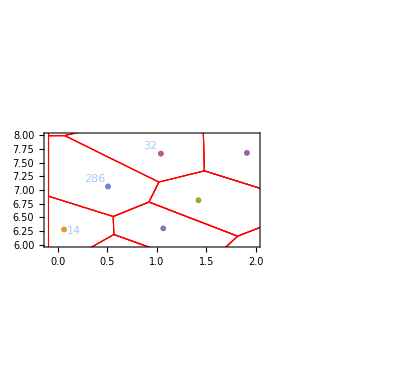

```mathematica
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{-0.1,2},{6,8}},Frame->True]
```

## Test C++ with mathematica

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc","Data"]
```

<|/BoxMatrix→NumericArray[…],/additionalData→NumericArray[…],/d2Edgammadgamma→NumericArray[…],/d2Eidgammadgamma→NumericArray[…],/meanQ→NumericArray[…],/overlap→NumericArray[…],/position→NumericArray[…],/time→NumericArray[…],/type→NumericArray[…],/velocity→NumericArray[…]|>

```mathematica
temp=getData["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc"];
p=temp[[3,1]];
```

```mathematica
Dimensions[p]
```

{100,2}

```mathematica
p[[35]]
```

{2.28329,5.29739}

```mathematica
(*Step 2:Create 8 copies of the points*)
copies=Table[p,9];

(*Step 3:Translate each copy to mimic periodic boundary conditions*)
translations={{0,0},{0,10},{10,0},{10,10},{-10,0},{0,-10},{-10,-10},{-10,10},{10,-10}};
translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];
p=Flatten[translatedCopies[[1]],1];
polygons=MeshPrimitives[vm,2];
```

```mathematica
min=Min[p]-.1;max=Max[p]+.1;
vm=VoronoiMesh[p,{{min,max},{min,max}}];
```

```mathematica
centroids=RegionCentroid/@MeshPrimitives[vm,2];
(*This gives the cell index with a given cell center*)
centroids=RegionCentroid/@MeshPrimitives[vm,2];
cellIndex=Table[Nearest[centroids->Automatic,p[[i]]][[1]],{i,1,Length[p]}];
polygons=MeshPrimitives[vm,2];
```

```mathematica
VareasI=PropertyValue[{vm,2},MeshCellMeasure];
VperisI=RegionMeasure/@(MeshPrimitives[vm,2]/.Polygon[{x_,y__}]:>Line[{x,y,x}]);
```

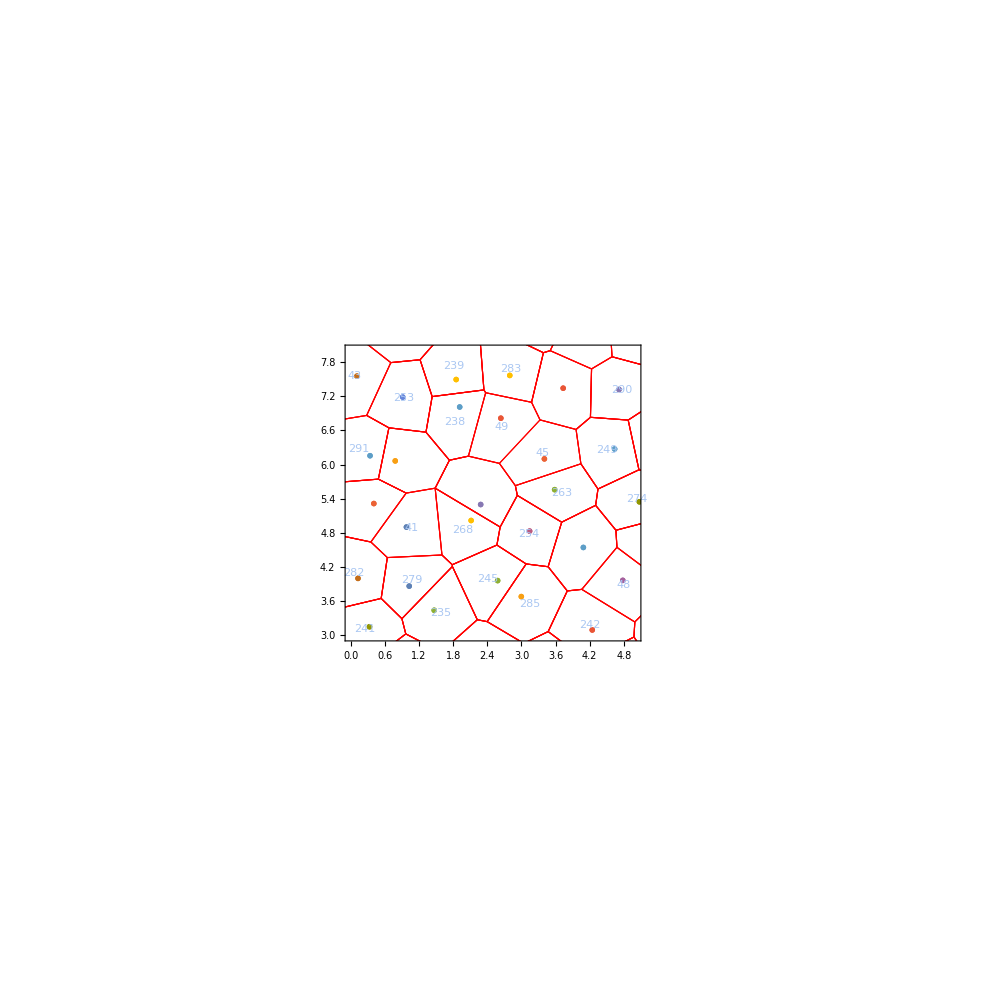

```mathematica
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{0,5},{3,8}},Frame->True]
```

```mathematica
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm0,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{0,5},{3,8}},Frame->True]
```

HighlightMesh::meshreg: Valid MeshRegion or BoundaryMeshRegion object expected at position 1 of HighlightMesh[EmptyRegion[2],{2,1,2}].

Show::gcomb: Could not combine the graphics objects in Show[HighlightMesh[EmptyRegion[2],{2,1,2}],,PlotRange→{{0,5},{3,8}},Frame→True].

Show[HighlightMesh[EmptyRegion[2],{2,1,2Index}],-Graphics-,PlotRange→{{0,5},{3,8}},Frame→True]

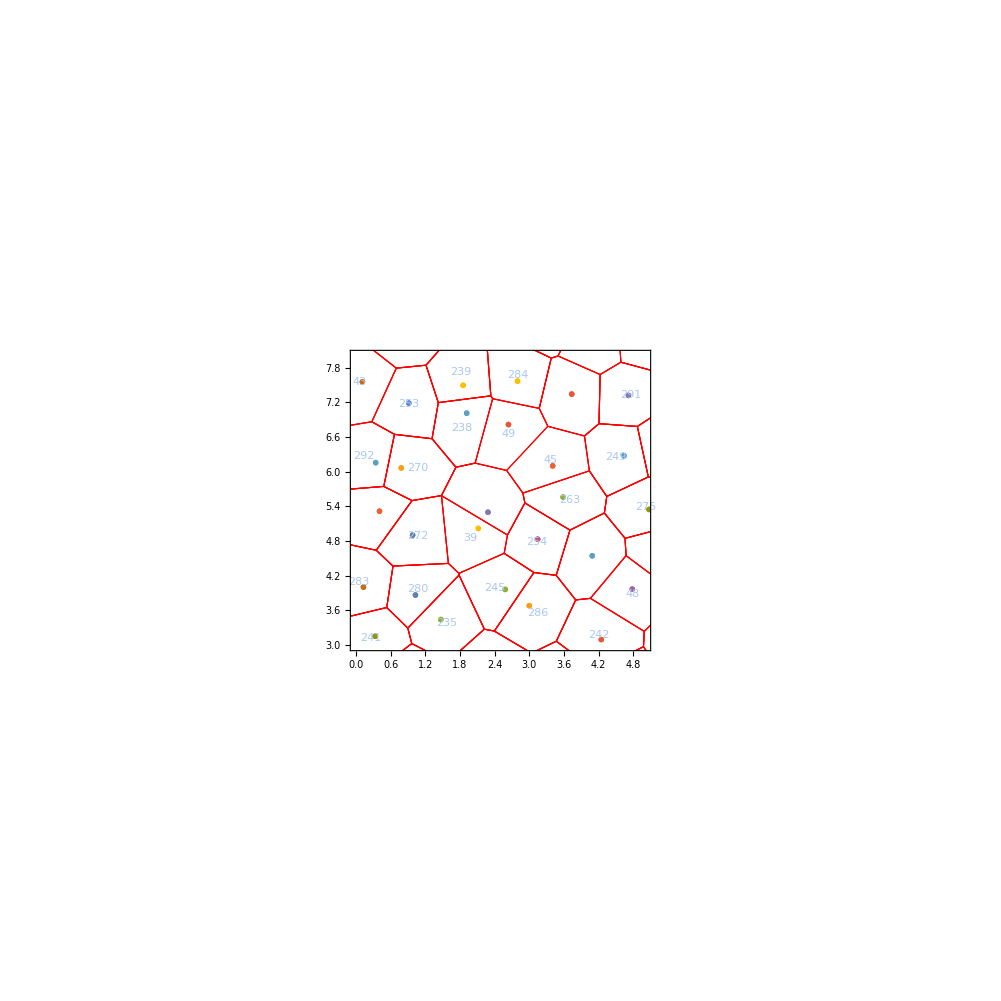

```mathematica
dl=ListPlot[Table[{p[[i]]},{i,1,Length[p]}],PlotMarkers->Table[i,{i,1,Length[p]}]];
Show[HighlightMesh[vm1,{Style[2,White],Style[1,Thick,Red],Labeled[2,"Index"]}],dl,PlotRange->{{0,5},{3,8}},Frame->True]
```

```mathematica
Vperis0[[754]]
```

4.07167

```mathematica
VperisI[[754]]
```

4.07203

```mathematica
((Vareas0[[754]]-1)^2+(Vperis0[[754]]-3.8)^2+(Vareas1[[887]]-1)^2+(Vperis1[[887]]-3.8)^2-2*((VareasI[[754]]-1)^2+(VperisI[[754]]-3.8)^2))/0.001/0.001
```

-269.235

```mathematica
((Vareas0[[754]]-1)^2+(Vareas1[[887]]-1)^2-2*((VareasI[[754]]-1)^2))/0.001/0.001
```

-0.0450433

```mathematica
((Vperis0[[754]]-3.8)^2+(Vperis1[[887]]-3.8)^2-2*(VperisI[[754]]-3.8)^2)/0.001/0.001
```

-269.19

```mathematica
Sum[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.00001,1,1,1,3.8],{i,1,100}]
```

72.3568

```mathematica
polygons[[1]][[1]]
```

{{4.01313,2.22287},{4.60219,1.96456},{4.82441,3.46132},{3.99491,3.36175}}

```mathematica
d2eidgdgGeneraliCenter[polygons[[322]][[1]],p[[1]],{594,25,81,85,58,592},1,1,1,3.8]
```

2.45173

```mathematica
Sum[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.001,1,1,1,3.8],{i,1,1}]
```

-2.51253×10^7

```mathematica
Vareas[[1]]
```

Part::partd: Part specification 0.848802⟦1⟧ is longer than depth of object.

0.848802⟦1⟧

```mathematica
numreicali=Table[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.001,1,1,1,3.8],{i,100}]
```

{0.447257,0.204348,0.331036,0.745252,-0.00192029,0.553292,0.0543144,-0.225381,0.228529,0.370602,2.00625,0.146055,0.689928,0.236455,1.60433,0.695891,2.73993,0.979374,-0.0288107,0.419283,1.76199,0.137478,0.41614,0.313545,0.113517,0.635357,1.15318,1.44353,-0.235517,0.968593,-0.0138495,2.15893,0.489653,0.444979,-269.235,0.279921,0.358613,0.247162,0.138725,1.59455,1.91523,2.4764,1.3715,0.880833,0.921265,0.346905,0.431784,0.333641,0.63612,0.324092,1.21224,0.771763,-332.65,0.479131,0.277354,0.484592,0.575443,-5.65466,0.685714,0.0962324,-156.733,0.605645,0.239041,0.408746,0.0176259,1.89134,0.959416,0.142456,-0.619451,1.03409,1.0491,1.63315,-0.0328832,1.96191,3.27352,0.260601,-0.335009,0.186584,1.13389,1.38022,1.06289,2.78147,0.858447,0.418076,0.0162496,0.979165,0.446485,1.17107,0.212631,-0.117373,-0.501297,0.104734,0.715656,1.52344,1.00326,0.453147,0.452548,0.674849,-0.0463613,1.4236}

```mathematica
numreicali[[61]]
```

-156.733

```mathematica
cellIndex[[35]]
```

754

```mathematica
Min[Table[numdericalCelli[i,cellIndex,cellIndex0,cellIndex1,0.001,1,1,1,3.8],{i,100}]]
```

-332.65

```mathematica
d2eidgdgEntire[p,Table[i,{i,100}],1,1,1,3.8]
```

72.3567

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc","Data"][[3]][[1]][[1]]
```

72.3567

```mathematica
d2eidgdgEach[p,Table[i,{i,100}],1,1,1,3.8]
```

{0.447255,0.204347,0.331035,0.745251,-0.00192178,0.553283,0.0543128,-0.225382,0.228526,0.370601,2.00625,0.146054,0.689925,0.23645,1.60433,0.695887,2.73992,0.979371,-0.0288111,0.419281,1.76198,0.137477,0.416137,0.313545,0.113515,0.635346,1.15317,1.44352,-0.235518,0.968591,-0.0138504,2.15892,0.489652,0.444977,1.06591,0.279918,0.358613,0.247162,0.138725,1.59454,1.91523,2.4764,1.37149,0.880831,0.921264,0.346904,0.431783,0.333638,0.636118,0.324092,1.21223,0.77176,0.508898,0.47913,0.277351,0.48459,0.575442,0.294295,0.685712,0.096232,2.84242,0.605645,0.23904,0.408744,0.0176248,1.89134,0.959414,0.142455,-0.619453,1.03408,1.04909,1.63314,-0.0328893,1.96191,3.27351,0.2606,-0.33501,0.186583,1.13389,1.38022,1.06289,2.78147,0.858441,0.418074,0.0162488,0.979159,0.446484,1.17107,0.212627,-0.117375,-0.501299,0.104734,0.715655,1.52343,1.00325,0.453146,0.452544,0.674848,-0.0463623,1.42359}

```mathematica
Normal[Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc","Data"][[4]][[1]]]
```

{0.447255,0.204347,0.331035,0.745251,-0.00192178,0.553283,0.0543128,-0.225382,0.228526,0.370601,2.00625,0.146054,0.689925,0.23645,1.60433,0.695887,2.73992,0.979371,-0.0288111,0.419281,1.76198,0.137477,0.416137,0.313545,0.113515,0.635346,1.15317,1.44352,-0.235518,0.968591,-0.0138504,2.15892,0.489652,0.444977,1.06591,0.279918,0.358613,0.247162,0.138725,1.59454,1.91523,2.4764,1.37149,0.880831,0.921264,0.346904,0.431783,0.333638,0.636118,0.324092,1.21223,0.77176,0.508898,0.47913,0.277351,0.48459,0.575442,0.294295,0.685712,0.096232,2.84242,0.605645,0.23904,0.408744,0.0176248,1.89134,0.959414,0.142455,-0.619453,1.03408,1.04909,1.63314,-0.0328893,1.96191,3.27351,0.2606,-0.33501,0.186583,1.13389,1.38022,1.06289,2.78147,0.858441,0.418074,0.0162488,0.979159,0.446484,1.17107,0.212627,-0.117375,-0.501299,0.104734,0.715655,1.52343,1.00325,0.453146,0.452544,0.674848,-0.0463623,1.42359}

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc","Data"][[3]][[1]][[1]]
```

72.3567

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/test_dE2Dgammadgamma.nc","Data"][[3]][[1]][[1]]
```

72.3567

```mathematica
Import["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/test_N100_p3.75000_T0.05000000_time100.nc","Datasets"]
```

{/d2Edgammadgamma}

```mathematica
temp=getData["/home/chengling/Research/Project/Cell/AnalyticalG/cellGPU/testData/test_N100_p3.75000_T0.05000000_time100.nc"];
p=temp[[3,1]];
```

Part::partw: Part 7 of … does not exist.

Part::partw: Part 2 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
copies=Table[p,9];

(*Step 3:Translate each copy to mimic periodic boundary conditions*)
translations={{0,0},{0,10},{10,0},{10,10},{-10,0},{0,-10},{-10,-10},{-10,10},{10,-10}};
translatedCopies=Table[Map[#+translation&,copies[[i]]],{i,1,9},{translation,translations}];
p=Flatten[translatedCopies[[1]],1];
polygons=MeshPrimitives[vm,2];
```

## Analytical form for C

```mathematica
(**)
```

```mathematica
r1={r1x,r1y};r2={r2x,r2y};r3={r3x,r3y};
```

```mathematica
Simplify[v2drirj[r2,r3,r1][[1,1,2]]r3[[2]]r2[[2]]/.{r1x->0,r1y->0}]
```

-(r2y r3y (r2y^3 r3x r3y-r2x^3 r3y^2+r2x r2y r3y (3 r2x r3x-3 r3x^2-r3y^2)+r2y^2 (r3x^3+r2x r3y^2-r3x r3y^2)))/(2 (r2y r3x-r2x r3y)^3)

```mathematica
dh2dgdgAna=Simplify[{(v2drirj[r1,r2,r3][[1,1,1]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,1]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,1]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,1]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,1]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,1]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,1]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,1]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,1]]r3[[2]])r3[[2]],(v2drirj[r1,r2,r3][[1,1,2]]r2[[2]])r1[[2]]+(v2drirj[r1,r3,r2][[1,1,2]]r3[[2]])r1[[2]]+(v2driri[r1,r2,r3][[1,1,2]]r1[[2]])r1[[2]]+(v2drirj[r2,r1,r3][[1,1,2]]r1[[2]])r2[[2]]+(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]+(v2driri[r2,r1,r3][[1,1,2]]r2[[2]])r2[[2]]+(v2drirj[r3,r1,r2][[1,1,2]]r1[[2]])r3[[2]]+(v2drirj[r3,r2,r1][[1,1,2]]r2[[2]])r3[[2]]+(v2driri[r3,r1,r2][[1,1,2]]r3[[2]])r3[[2]]}]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}
```

{((r1y-r2y) (r1y-r3y) (r2y-r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3y+2 r2y r3x r3y+2 r1y (r2x r2y-r3x r3y+r1x (-r2y+r3y))+(-r2x+r3x) (r1y r1y)-r3x (r2y r2y)+r1x (r2y r2y-r3y r3y)+r2x (r3y r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y)}

```mathematica
CForm[dh2dgdgAna]
```

List(((r1y - r2y)*(r1y - r3y)*(r2y - r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y),
   (-2*r2x*r2y*r3y + 2*r2y*r3x*r3y + 2*r1y*(r2x*r2y - r3x*r3y + r1x*(-r2y + r3y)) + (-r2x + r3x)*(r1y*r1y) - r3x*(r2y*r2y) + 
      r1x*(r2y*r2y - r3y*r3y) + r2x*(r3y*r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y))

```mathematica
dh2dgdgAnaTest=Simplify[(v2drirj[r2,r3,r1][[1,1,2]]r3[[2]])r2[[2]]]
```

(r2y r3y (-r2y^2 r3x^3-3 r2x^2 r2y r3x r3y-r2y^3 r3x r3y+3 r2x r2y r3x^2 r3y+r2x^3 r3y^2-r2x r2y^2 r3y^2+r2y^2 r3x r3y^2+r2x r2y r3y^3))/(2 (r2y r3x-r2x r3y)^3)

```mathematica
dhdgAna=Simplify[(v1dri[r1,r2,r3].{r1[[2]],0})+(v1dri[r2,r1,r3].{r2[[2]],0})+(v1dri[r3,r1,r2].{r3[[2]],0})]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}
```

{(r1x r1y (r2y-r3y)+r2y (r2x-r3x) r3y+r1y (-r2x r2y+r3x r3y))/(-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y),(-2 r2x r2y r3x+2 r2x r3x r3y+2 r1x (r2x r2y+r1y (-r2x+r3x)-r3x r3y)+(-r2y+r3y) (r1x r1x)+(-r2y+r3y) (r1y r1y)-r3y (r2x r2x)-r3y (r2y r2y)+r2y (r3x r3x)+r1y (r2x r2x+r2y r2y-r3x r3x-r3y r3y)+r2y (r3y r3y))/(2 (-r2y r3x+r1y (-r2x+r3x)+r1x (r2y-r3y)+r2x r3y))}

```mathematica
CForm[dhdgAna]
```

List((r1x*r1y*(r2y - r3y) + r2y*(r2x - r3x)*r3y + r1y*(-(r2x*r2y) + r3x*r3y))/(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y),
   (-2*r2x*r2y*r3x + 2*r2x*r3x*r3y + 2*r1x*(r2x*r2y + r1y*(-r2x + r3x) - r3x*r3y) + (-r2y + r3y)*(r1x*r1x) + (-r2y + r3y)*(r1y*r1y) - 
      r3y*(r2x*r2x) - r3y*(r2y*r2y) + r2y*(r3x*r3x) + r1y*(r2x*r2x + r2y*r2y - r3x*r3x - r3y*r3y) + r2y*(r3y*r3y))/
    (2.*(-(r2y*r3x) + r1y*(-r2x + r3x) + r1x*(r2y - r3y) + r2x*r3y)))

```mathematica
originalh=voro[p[[816]],p[[521]],p[[466]]]
```

```mathematica
test1[{r1x_,r1y_},{r2x_,r2y_},{r3x_,r3y_}]:=(r1x*r1y*(r2y-r3y)+r2y*(r2x-r3x)*r3y+r1y*(-(r2x*r2y)+r3x*r3y))/(-(r2y*r3x)+r1y*(-r2x+r3x)+r1x*(r2y-r3y)+r2x*r3y);
testr1=p[[816]]-p[[521]];
testr2=p[[466]]-p[[521]];
test1[p[[521]]-{1,1},p[[816]]-{1,1},p[[466]]-{1,1}]
```

16.2053

```mathematica
p[[521]]-p[[816]]
```

{-0.469041,1.00448}

```mathematica
CForm[Simplify[e2dh1h1[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*((-(((h1x - h2x)*(h1x - h2x))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) + 
          1/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) - 
          ((h1x - h6x)*(h1x - h6x))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5) + 
          1/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
       (0.5*h2y - 0.5*h6y)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
    2*((-0.5*h2x + 0.5*h6x)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1x - h2x)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) - 
          ((h1x - h6x)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))),
   List(2*((-0.5*h2x + 0.5*h6x)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1x - h2x)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) - 
          ((h1x - h6x)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))),
    2*((0.5*h2x - 0.5*h6x)*(0.5*h2x - 0.5*h6x) + ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))) + 
       (-(((h1y - h2y)*(h1y - h2y))/Power((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y),1.5)) + 
          1/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) - 
          ((h1y - h6y)*(h1y - h6y))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5) + 
          1/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        (-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
          Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
          Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))))

```mathematica
(*dedh,d2edhdh*)
```

```mathematica
Simplify[e2dh1h1[{h1,h2,h3,h4,h5,h6}]][[1]][[1]]
```

2 (((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2)))^2+(-(h1x-h2x)^2/(((h1x-h2x)^2+(h1y-h2y)^2)^(3/2))+1/(√((h1x-h2x)^2+(h1y-h2y)^2))-(h1x-h6x)^2/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2))+1/(√((h1x-h6x)^2+(h1y-h6y)^2))) (-4+√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2))+(0.5 h2y-0.5 h6y)^2)

```mathematica
Simplify[e2dh1h6[{h1,h2,h3,h4,h5,h6}]][[1]][[1]]
```

2 (((h1x-h2x)/(√((h1x-h2x)^2+(h1y-h2y)^2))+(h1x-h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2))) ((-h1x+h6x)/(√((h1x-h6x)^2+(h1y-h6y)^2))+(-h5x+h6x)/(√((h5x-h6x)^2+(h5y-h6y)^2)))-1/(((h1x-h6x)^2+(h1y-h6y)^2)^(3/2))(-4+√((h1x-h2x)^2+(h1y-h2y)^2)+√((h2x-h3x)^2+(h2y-h3y)^2)+√((h3x-h4x)^2+(h3y-h4y)^2)+√((h4x-h5x)^2+(h4y-h5y)^2)+√((h1x-h6x)^2+(h1y-h6y)^2)+√((h5x-h6x)^2+(h5y-h6y)^2)) (h1y-h6y)^2+(0.5 h1y-0.5 h5y) (0.5 h2y-0.5 h6y))

```mathematica
CForm[Simplify[e2dh1h3[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(-0.5*h2y + 0.5*h4y)*(0.5*h2y - 0.5*h6y) + 2*
      ((-h2x + h3x)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3x - h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h2x - 0.5*h4x)*(0.5*h2y - 0.5*h6y) + 2*((-h2y + h3y)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3y - h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
   List(2*(-0.5*h2y + 0.5*h4y)*(-0.5*h2x + 0.5*h6x) + 2*((-h2x + h3x)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3x - h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h2x - 0.5*h4x)*(-0.5*h2x + 0.5*h6x) + 2*((-h2y + h3y)/Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + 
        (h3y - h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h4[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(-0.5*h3y + 0.5*h5y)*(0.5*h2y - 0.5*h6y) + 2*
      ((-h3x + h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4x - h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h3x - 0.5*h5x)*(0.5*h2y - 0.5*h6y) + 2*((-h3y + h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4y - h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))),
   List(2*(-0.5*h3y + 0.5*h5y)*(-0.5*h2x + 0.5*h6x) + 2*((-h3x + h4x)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4x - h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y))),
    2*(0.5*h3x - 0.5*h5x)*(-0.5*h2x + 0.5*h6x) + 2*((-h3y + h4y)/Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
        (h4y - h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)))*
      ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h5[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*(0.5*h2y - 0.5*h6y)*(-0.5*h4y + 0.5*h6y) + 2*
      ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4x + h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5x - h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))),
    2*(0.5*h4x - 0.5*h6x)*(0.5*h2y - 0.5*h6y) + 2*((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4y + h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5y - h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))),
   List(2*(-0.5*h2x + 0.5*h6x)*(-0.5*h4y + 0.5*h6y) + 2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4x + h5x)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5x - h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))),
    2*(0.5*h4x - 0.5*h6x)*(-0.5*h2x + 0.5*h6x) + 2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h4y + h5y)/Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + 
        (h5y - h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y)))))

```mathematica
CForm[Simplify[e2dh1h6[{h1,h2,h3,h4,h5,h6}]]//.{x_^2:>HoldForm[x*x],x_^3:>HoldForm[x*x*x]}]
```

List(List(2*((0.5*h1y - 0.5*h5y)*(0.5*h2y - 0.5*h6y) + ((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((-h1x + h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          (-h5x + h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) - 
       ((h1y - h6y)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
            Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
            Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
            Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5)),
    1. + 0.5*h1y*h2x - 0.5*h1x*h2y + 0.5*h2y*h3x - 0.5*h2x*h3y + 0.5*h3y*h4x - 0.5*h3x*h4y + 0.5*h4y*h5x - 0.5*h4x*h5y - 0.5*h1y*h6x + 
     0.5*h5y*h6x + 2*(-0.5*h1x + 0.5*h5x)*(0.5*h2y - 0.5*h6y) + 0.5*h1x*h6y - 0.5*h5x*h6y + 
     2*((h1x - h2x)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1x - h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h1y + h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
        (-h5y + h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
     (2*(h1x - h6x)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
          Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5)),
   List(-1. - 0.5*h1y*h2x + 0.5*h1x*h2y - 0.5*h2y*h3x + 0.5*h2x*h3y - 0.5*h3y*h4x + 0.5*h3x*h4y - 0.5*h4y*h5x + 0.5*h4x*h5y + 
     2*(0.5*h1y - 0.5*h5y)*(-0.5*h2x + 0.5*h6x) + 0.5*h1y*h6x - 0.5*h5y*h6x - 0.5*h1x*h6y + 0.5*h5x*h6y + 
     2*((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
        (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
      ((-h1x + h6x)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
        (-h5x + h6x)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) + 
     (2*(h1x - h6x)*(h1y - h6y)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
          Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5),
    2*((-0.5*h1x + 0.5*h5x)*(-0.5*h2x + 0.5*h6x) + ((h1y - h2y)/Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
          (h1y - h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)))*
        ((-h1y + h6y)/Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
          (-h5y + h6y)/Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))) - 
       ((h1x - h6x)*(h1x - h6x)*(-4 + Sqrt((h1x - h2x)*(h1x - h2x) + (h1y - h2y)*(h1y - h2y)) + 
            Sqrt((h2x - h3x)*(h2x - h3x) + (h2y - h3y)*(h2y - h3y)) + Sqrt((h3x - h4x)*(h3x - h4x) + (h3y - h4y)*(h3y - h4y)) + 
            Sqrt((h4x - h5x)*(h4x - h5x) + (h4y - h5y)*(h4y - h5y)) + Sqrt((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y)) + 
            Sqrt((h5x - h6x)*(h5x - h6x) + (h5y - h6y)*(h5y - h6y))))/Power((h1x - h6x)*(h1x - h6x) + (h1y - h6y)*(h1y - h6y),1.5))))

## Useless garbage

```mathematica
polygonOri=Polygon[polygons[[138]][[1]]];
(*Measure the area*)
areaOri=Area[polygonOri]
(*Measure the perimeter*)
perimeterOri=Perimeter[polygonOri]
epolyOri=(areaOri-1)^2+(perimeterOri-4)^2
```

0.836199

3.5216

0.255696

```mathematica
polygonsback=polygons[[138]][[1]];
polygonsback[[1]]=strainback.polygons[[138]][[1]][[1]];
polygonback=Polygon[polygonsback];
areaback=Area[polygonback]
(*Measure the perimeter*)
perimeterback=Perimeter[polygonOri]
epolyback=(areaback-1)^2+(perimeterback-4)^2
```

0.828279

3.5216

0.258353

```mathematica
polygonsfor=polygons[[138]][[1]];
polygonsfor[[1]]=strainfor.polygons[[138]][[1]][[1]];
polygonfor=Polygon[polygonsfor];
areafor=Area[polygonfor]
(*Measure the perimeter*)
perimeterfor=Perimeter[polygonfor]
epolyfor=(areafor-1)^2+(perimeterfor-4)^2
```

0.84412

3.53901

0.236809

```mathematica
dedrirj[r1_,r2_,r3_]:={{{D[D[hijk[[1]],rix],rjx],D[D[hijk[[2]],rix],rjx]},
{D[D[hijk[[1]],riy],rjx],D[D[hijk[[2]],riy],rjx]}},
{{D[D[hijk[[1]],rix],rjy],D[D[hijk[[2]],rix],rjy]},
{D[D[hijk[[1]],riy],rjy],D[D[hijk[[2]],riy],rjy]}}}/.{rix->r1[[1]],riy->r1[[2]],rjx->r2[[1]],rjy->r2[[2]],rkx->r3[[1]],rky->r3[[2]]};
```

```mathematica
strainTest={{1,gg},{0,1}};
D[Sqrt[(strainTest.r1-strainTest.r2).(strainTest.r1-strainTest.r2)],gg]
```

((r1y-r2y) (r1x+gg r1y-r2x-gg r2y))/(√((r1y-r2y)^2+(r1x+gg r1y-r2x-gg r2y)^2))